## Pure functions

```mathematica
#^2+1 &[5]
```

26

```mathematica
ff[x_]:= x^2+1
```

```mathematica
ff[5]
```

26

```mathematica
Select[{1,2,3,4,5,6,7,8,9,10},Cos[ #] >Sin[#] & ]
```

{4,5,6,7}

```mathematica
#>3 &[4]
```

True

```mathematica
Map[#^2&,{1,2,3,4,5}]
```

{1,4,9,16,25}

```mathematica
#^2&/@{1,2,3,4,5}
```

{1,4,9,16,25}

```mathematica
Framed[#] & /@ List[#]&/@ (#^2)&/@{a,b,c}
```

{{a^2},{b^2},{c^2}}

```mathematica
(*выделяй тело функции с # скобками!*)
```

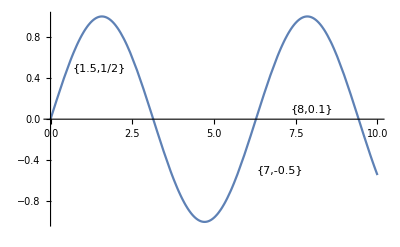

```mathematica
Plot[Sin[x],{x,0,10},Epilog->((Text[#,#])& /@ {{1.5,1/2},{7,-0.5},{8,0.1}})]
```

#### Задание чистой функции через Function

```mathematica
Function[#^2+1][x]
```

1+x^2

```mathematica
(#^2+1) &[x]
```

1+x^2

```mathematica
Function[{x},x^2+Sin[x]][1.1]
```

2.10121

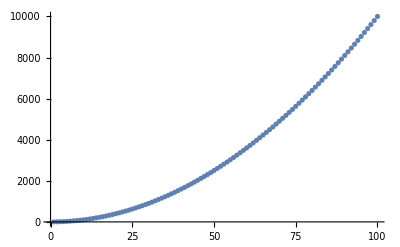

```mathematica
ListPlot[Function[{x},{x,N[x^2+Sin[x]]}]/@Range[100]]
```

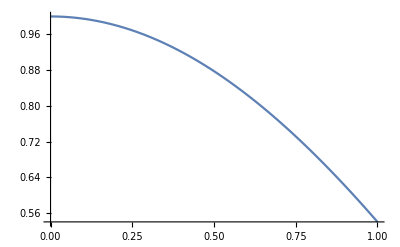
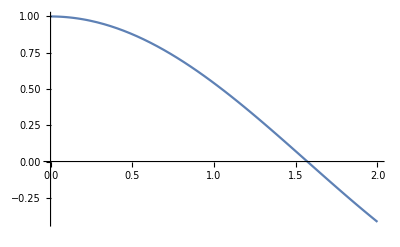
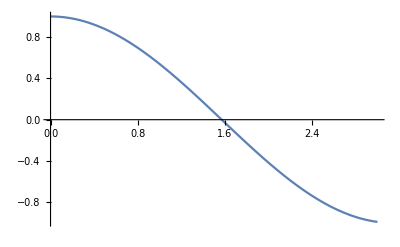

```mathematica
Function[{x}, Plot[Cos[y],{y,0,x}],{Listable}][{1,2,3}]
```

```mathematica
(#,Plot[Cos[y],{y,0,#}],{Listable}) & [{1,2,3}]
```

Syntax::sntxf: "(" cannot be followed by "#,Plot[Cos[y],{y,0,#}],{Listable})".

```mathematica
.10Чистые функции с более чем одним аргументом
```

```mathematica
#1+#2&[x,y]
```

x+y

```mathematica
#1+#2^(#1+#2)&[x,y]
```

x+y^(x+y)

```mathematica
Function[{x,y,z},x^2+y/z][x,1,Cos[x]]
```

x^2+Sec[x]

#### Чистые фунции с произвольным количеством аргументов

```mathematica
## & [x,y,z,t]
```

Sequence[x,y,z,t]

```mathematica
{1,2,Sequence[x,y,z,t]}
```

{1,2,x,y,z,t}

```mathematica
f[Sequence[x,y,z,t]]
```

f[x,y,z,t]

```mathematica
{a,b,##,A,V,##}&[x,y,z,t,5,5,5,5,5,5,4,2,32,6,5]
```

{a,b,x,y,z,t,5,5,5,5,5,5,4,2,32,6,5,A,V,x,y,z,t,5,5,5,5,5,5,4,2,32,6,5}

```mathematica
{##10} &[x,y,z,t,1,2,3,4,2,3,42]
```

{3,42}